```mathematica
Clear["Global`*"]
```

```mathematica
f[r_]:=1-2 M/r;
g=({{-f[r], 0, 0, 0}, {0, 1/f[r], 0, 0}, {0, 0, r^2, 0}, {0, 0, 0, r^2 Sin[θ]^2}});
ig=Inverse[g];
sqrg=Assuming[{r>0,Sin[θ]>0},Simplify[√(-Det[g])]];
```

```mathematica
H[σ_]:=(2M)/1(Log[1-σ]-1/σ+Log[σ]);
t$coord=1(τ-H[σ]);
r$coord=(2M)/σ;
θ$coord=ArcCos[-x];
HPHC$coord={τ,σ,x,ϕ};
S2H=({{D[t$coord, τ], D[t$coord, σ], 0, 0}, {0, D[r$coord, σ], 0, 0}, {0, 0, D[θ$coord, x], 0}, {0, 0, 0, 1}})
```

{{1,-2 M (-1/(1-σ)+1/σ^2+1/σ),0,0},{0,-(2 M)/σ^2,0,0},{0,0,1/(√(1-x^2)),0},{0,0,0,1}}

```mathematica
g$HPHC=Table[Sum[S2H[[ac,Ac]]S2H[[bc,Bc]]g[[ac,bc]],{ac,4},{bc,4}],{Ac,4},{Bc,4}]/.{r->r$coord,θ->θ$coord}//Simplify;
ig$HPHC=Inverse[g$HPHC]//Simplify;
sqrg$HPHC=Assuming[{M>0,λ>0,σ>0},Simplify[√(-Det[g$HPHC])]];
```

```mathematica
g$HPHC
```

{{-1+σ,2 M (-2+1/σ^2),0,0},{2 M (-2+1/σ^2),(16 M^2 (1+σ))/σ^2,0,0},{0,0,-(4 M^2)/((-1+x^2) σ^2),0},{0,0,0,-(4 M^2 (-1+x^2))/σ^2}}

```mathematica
ig$HPHC
```

{{-4 σ^2 (1+σ),(σ^2-2 σ^4)/(2 M),0,0},{(σ^2-2 σ^4)/(2 M),-((-1+σ) σ^4)/(4 M^2),0,0},{0,0,-((-1+x^2) σ^2)/(4 M^2),0},{0,0,0,-σ^2/(4 M^2 (-1+x^2))}}

```mathematica
Sum[σ D[(sqrg$HPHC*ig$HPHC[[ac,bc]]D[(σ/(2M)Φ[τ,σ,x,ϕ]), HPHC$coord[[bc]]]), HPHC$coord[[ac]]],{ac,4},{bc,4}]/.{Φ_[τ,σ,x,ϕ]->Φ}//FullSimplify//Collect[#,{Derivative[2,0,0,0][Φ],Derivative[1,1,0,0][Φ],Derivative[0,2,0,0][Φ],Derivative[1,0,0,0][Φ],Derivative[0,0,2,0][Φ]}]&
```

-σ Φ-Φ^(0,0,0,2)/(-1+x^2)-2 x Φ^(0,0,1,0)+(1-x^2) Φ^(0,0,2,0)+(2-3 σ) σ Φ^(0,1,0,0)+(1-σ) σ^2 Φ^(0,2,0,0)-8 M σ Φ^(1,0,0,0)+4 M (1-2 σ^2) Φ^(1,1,0,0)-16 M^2 (1+σ) Φ^(2,0,0,0)

```mathematica
(*  *)
```

```mathematica
Sum[1/sqrg$HPHC D[(sqrg$HPHC*ig$HPHC[[ac,bc]]D[(σ/(2M)Φ[σ,x] ⅇ^(-I(ω τ-m ϕ))), HPHC$coord[[bc]]]), HPHC$coord[[ac]]],{ac,4},{bc,4}]/.{Φ_[σ,x]->Φ}/.{ω->I s}//FullSimplify
```

-1/(8 M^3 (-1+x^2))ⅇ^(s τ+ⅈ m ϕ) σ^3 (-m^2 Φ+(-1+x) (1+x) (σ+8 M s (σ+2 M s (1+σ))) Φ+2 x (-1+x^2) Φ^(0,1)+(-1+x^2)^2 Φ^(0,2)+(-1+x^2) ((-4 M s-2 σ+(3+8 M s) σ^2) Φ^(1,0)+(-1+σ) σ^2 Φ^(2,0)))

```mathematica
mastereq=(-1+x^2)^-1*(-m^2 Φ+(-1+x) (1+x) (σ+8 M s (σ+2 M s (1+σ))) Φ+2 x (-1+x^2) Derivative[0,1][Φ]+(-1+x^2)^2 Derivative[0,2][Φ]+(-1+x^2) ((-4 M s-2 σ+(3+8 M s) σ^2) Derivative[1,0][Φ]+(-1+σ) σ^2 Derivative[2,0][Φ]))//Simplify
```

-(m^2 Φ)/(-1+x^2)+(σ+8 M s σ+16 M^2 s^2 (1+σ)) Φ+2 x Φ^(0,1)+(-1+x^2) Φ^(0,2)+(-4 M s-2 σ+(3+8 M s) σ^2) Φ^(1,0)+(-1+σ) σ^2 Φ^(2,0)

```mathematica
(*  *)
```

```mathematica
Sum[1/sqrg$HPHC D[(sqrg$HPHC*ig$HPHC[[ac,bc]]D[(σ/(2M)Φ[σ,x] ⅇ^(-I(ω τ-m ϕ))(1-x^2)^(-m/2)), HPHC$coord[[bc]]]), HPHC$coord[[ac]]],{ac,4},{bc,4}]/.{Φ_[σ,x]->Φ}/.{ω->I s}//FullSimplify
```

-(ⅇ^(s τ+ⅈ m ϕ) (1-x^2)^(-m/2) σ^3 (((-1+m) m+σ+8 M s (σ+2 M s (1+σ))) Φ-2 (-1+m) x Φ^(0,1)+(-1+x^2) Φ^(0,2)+(-4 M s-2 σ+(3+8 M s) σ^2) Φ^(1,0)+(-1+σ) σ^2 Φ^(2,0)))/(8 M^3)

```mathematica
reseq=(((-1+m) m+σ+8 M s (σ+2 M s (1+σ))) Φ-2 (-1+m) x Derivative[0,1][Φ]+(-1+x^2) Derivative[0,2][Φ]+(-4 M s-2 σ+(3+8 M s) σ^2) Derivative[1,0][Φ]+(-1+σ) σ^2 Derivative[2,0][Φ])//Simplify
```

((-1+m) m+σ+8 M s (σ+2 M s (1+σ))) Φ-2 (-1+m) x Φ^(0,1)+(-1+x^2) Φ^(0,2)+(-4 M s-2 σ+(3+8 M s) σ^2) Φ^(1,0)+(-1+σ) σ^2 Φ^(2,0)

```mathematica
Cheb[n_,Z1_,Z2_,myPrec_:MachinePrecision]:=Module[{b,c,d,x},
b=Z2-Z1;(* b为区间长度 *)
x=N[Table[Cos[(i π)/(n-1)],{i,0,n-1}],myPrec];
x=b/2(x+1)+Z1;
c=Table[1,{i,1,n}];c[[1]]=2;c[[-1]]=2;
d=N[2/b Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}],myPrec];
(* d是Chebyshev求导矩阵*)
d=d-DiagonalMatrix[Total[d,{2}]];
Return[{d,x}]
];
```

#### modes with

```mathematica
mastereq/.{s->0,m->0}
```

σ Φ+2 x Φ^(0,1)+(-1+x^2) Φ^(0,2)+(-2 σ+3 σ^2) Φ^(1,0)+(-1+σ) σ^2 Φ^(2,0)

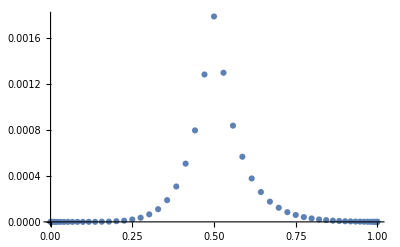

```mathematica
nσ=55;
dσ=Cheb[nσ,0,1][[1]];
σσ=Cheb[nσ,0,1][[2]];
Al=DiagonalMatrix[σσ+l(l+1)]+DiagonalMatrix[(-2 σσ+3 σσ^2)] .dσ+DiagonalMatrix[(-1+σσ) σσ^2 ] .dσ.dσ/.l->10(* A is singular when l=0*);
b=0*σσ;b[[(nσ+1)/2]]=1;
Phi =LinearSolve[Al,b];
ListPlot[{Transpose[{σσ,Phi}]},PlotRange->All]
(*ListPlot[{Transpose[{σσ,Al.Phi}]},PlotRange->All]*)
```

§ a key observation: , because the equation reduces to .

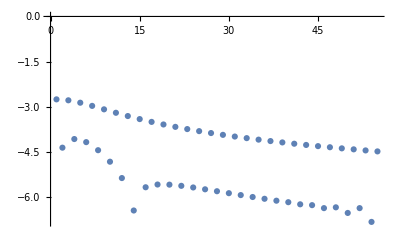

```mathematica
ListPlot[Log10[Abs[FourierDCT[Phi ,1]]]]
```

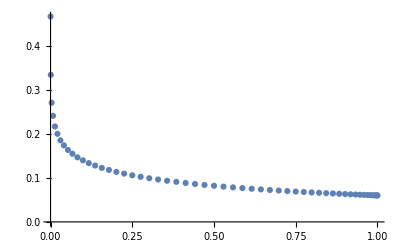

```mathematica
Al0=DiagonalMatrix[σσ]+DiagonalMatrix[(-2 σσ+3 σσ^2)] .dσ+DiagonalMatrix[(-1+σσ) σσ^2 ] .dσ.dσ;
zeroMode$σ=NullSpace[Al0][[1]];
ListPlot[{Transpose[{σσ,NullSpace[Al0][[1]]}]},PlotRange->All]
```

```mathematica
Eigenvalues[Al0]
```

{10879.2,9215.54,8159.14,7323.75,6622.53,6016.01,5481.75,5005.35,4576.82,4188.83,3835.79,3513.3,3217.83,2946.46,2696.75,2466.62,2254.3,2058.25,1877.11,1709.7,1554.95,1411.91,1279.73,1157.63,1044.92,940.959,845.15,756.956,675.879,601.457,533.263,470.896,413.985,362.18,315.155,272.601,234.23,199.766,168.952,141.542,117.302,96.0095,77.4523,61.4272,47.739,36.1998,26.6282,18.8481,12.6877,7.97943,4.56151,2.28642,0.984151,0.275775,0.}

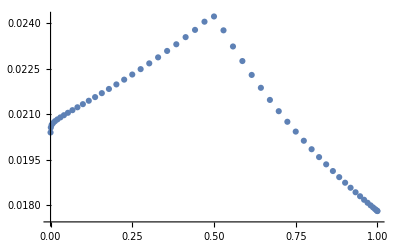

```mathematica
(* regular condition at  *)
Al0[[-1,;;]]=-2*dσ[[-1,;;]]+1;
(*MatrixRank[Al0]*)
(* , *)
δ0=1/2 Sin[π/2];
b=0*σσ;b[[(nσ+1)/2]]=1*δ0;
Phi0 =LinearSolve[Al0,b];
ListPlot[{Transpose[{σσ,Phi0}]},PlotRange->All]
```

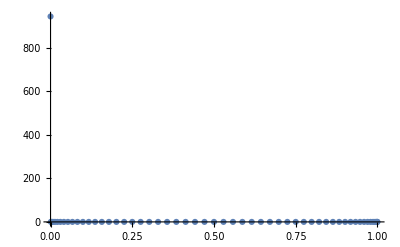

```mathematica
ListPlot[{Transpose[{σσ,Al0.zeroMode$σ}]},PlotRange->All]
```

```mathematica
Eigenvalues[Al0]
```

{10879.3,9215.59,8159.29,7780.28,7323.65,6622.49,6015.98,5481.73,5005.34,4576.81,4188.82,3835.78,3513.29,3217.83,2946.45,2696.74,2466.61,2254.29,2058.24,1877.1,1709.69,1554.94,1411.9,1279.72,1157.63,1044.92,940.951,845.141,756.946,675.869,601.447,533.252,470.884,413.972,362.165,315.139,272.583,234.21,199.744,168.927,141.513,117.269,95.9709,77.4071,61.3736,47.6746,36.1217,26.5321,18.7288,12.5389,7.79523,4.34109,2.05532,0.785466,0.110672}

```mathematica
nσ=49;
dσ=Cheb[nσ,0,1][[1]];
σσ=Cheb[nσ,0,1][[2]];
nx=33;
dx=Cheb[nx,-1,1][[1]];
xx=Cheb[nx,-1,1][[2]];
```

```mathematica
mastereq/.{s->0,m->0}
```

σ Φ+2 x Φ^(0,1)+(-1+x^2) Φ^(0,2)+(-2 σ+3 σ^2) Φ^(1,0)+(-1+σ) σ^2 Φ^(2,0)

```mathematica
Aσ=DiagonalMatrix[σσ]+DiagonalMatrix[(-2 σσ+3 σσ^2)] .dσ+DiagonalMatrix[(-1+σσ) σσ^2 ] .dσ.dσ;
Ax=DiagonalMatrix[2*xx].dx+DiagonalMatrix[(-1+xx^2)].dx.dx;
(*  *)
A=KroneckerProduct[Aσ,IdentityMatrix[nx]]+KroneckerProduct[IdentityMatrix[nσ],Ax];
```

```mathematica
MatrixRank[A]
```

1616

```mathematica
Dimensions[A]
```

{1617,1617}

```mathematica
MatrixRank[Ax]
```

32

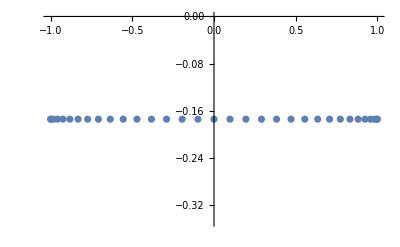

```mathematica
ListPlot[{Transpose[{xx,NullSpace[Ax][[1]]}]},PlotRange->All]
```

```mathematica
zeroMode=(KroneckerProduct[NullSpace[Aσ][[1]],NullSpace[Ax][[1]]]//Flatten) ;
ListPlot3D[Transpose[{KroneckerProduct[σσ,0*xx+1]//Flatten,KroneckerProduct[0*σσ+1,xx]//Flatten,Abs[zeroMode]}],PlotRange->All,PlotTheme->"Scientific",ColorFunction->"RedBlueTones",PlotLegends->Automatic,Boxed->True,Axes->True,AxesLabel->{"σ","x","Φ"},AxesStyle->Directive[Black,Thick]]
```

-Graphics3D-

Thus, the boundary condition at σ = 0 is

```mathematica
tmp=IdentityMatrix[nσ];tmp[[-1,-1]]=0;
Aσ[[-1,-1]]=1;
Am0=KroneckerProduct[Aσ,IdentityMatrix[nx]]+KroneckerProduct[tmp,Ax];
bσ=0*σσ;bσ[[(nσ+1)/2]]=1;
(* *)
bx=0*xx;bx[[(nx+1)/2]]=1;
bm0=KroneckerProduct[bσ,bx]//Flatten;
bm0[[-(nx);;-1]]=0*bm0[[-(nx);;-1]]+Phi0[[-1]];
Φm0 =LinearSolve[Am0,bm0];
ListPlot3D[Transpose[{KroneckerProduct[σσ,0*xx+1]//Flatten,KroneckerProduct[0*σσ+1,xx]//Flatten,Abs[Φm0] }],PlotRange->All,PlotTheme->"Scientific",ColorFunction->"RedBlueTones",PlotLegends->Automatic,Boxed->True,Axes->True,AxesLabel->{"σ","x","Φ"},AxesStyle->Directive[Black,Thick]]
```

-Graphics3D-

```mathematica
reseq
```

((-1+m) m+σ+8 M s (σ+2 M s (1+σ))) Φ-2 (-1+m) x Φ^(0,1)+(-1+x^2) Φ^(0,2)+(-4 M s-2 σ+(3+8 M s) σ^2) Φ^(1,0)+(-1+σ) σ^2 Φ^(2,0)

```mathematica
nσ=49;
dσ=Cheb[nσ,0,1][[1]];
σσ=Cheb[nσ,0,1][[2]];
nx=43;
dx=Cheb[nx,-1,1][[1]];
xx=Cheb[nx,-1,1][[2]];
rule$m={m->1};
rule$s={s->-I m Ω}/.rule$m/.{Ω->1};
```

```mathematica
Aσm=DiagonalMatrix[σσ+8 s (σσ+2 s (1+σσ))]+DiagonalMatrix[(-4 s-2 σσ+(3+8s) σσ^2)] .dσ+DiagonalMatrix[(-1+σσ) σσ^2 ] .dσ.dσ/.rule$s;
Axm=(-1+m) mIdentityMatrix[nx]+DiagonalMatrix[-2 (-1+m)*xx].dx+DiagonalMatrix[(-1+xx^2)].dx.dx/.rule$m;
Axm[[1,;;]]=0*Axm[[1,;;]];Axm[[1,1]]=1;
Axm[[-1,;;]]=0*Axm[[-1,;;]];Axm[[-1,-1]]=1;
(*  *)
tmp=IdentityMatrix[nx];tmp[[1,1]]=0;tmp[[-1,-1]]=0;
Am=KroneckerProduct[tmp,Aσm]+KroneckerProduct[Axm,IdentityMatrix[nσ]];
```

```mathematica
MatrixRank[Aσm]
```

49

```mathematica
MatrixRank[Axm]
```

43

```mathematica
nσ*nx
```

2107

```mathematica
MatrixRank[Am]
```

2107

```mathematica
bσ=0*σσ;bσ[[(nσ+1)/2]]=1;
bx=0*xx;bx[[(nx+1)/2]]=1;
bm=KroneckerProduct[bx,bσ]//Flatten;
Φm =LinearSolve[Am,bm];
ListPlot3D[Transpose[{KroneckerProduct[0*xx+1,σσ]//Flatten,KroneckerProduct[xx,0*σσ+1]//Flatten,Abs[Φm] }],PlotRange->All,PlotTheme->"Scientific",ColorFunction->"RedBlueTones",PlotLegends->Automatic,Boxed->True,Axes->True,AxesLabel->{"σ","x","Φ"},AxesStyle->Directive[Black,Thick]]
```

-Graphics3D-